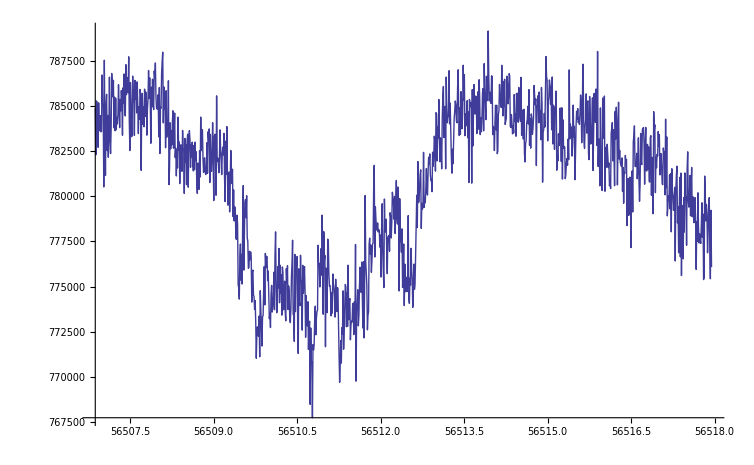

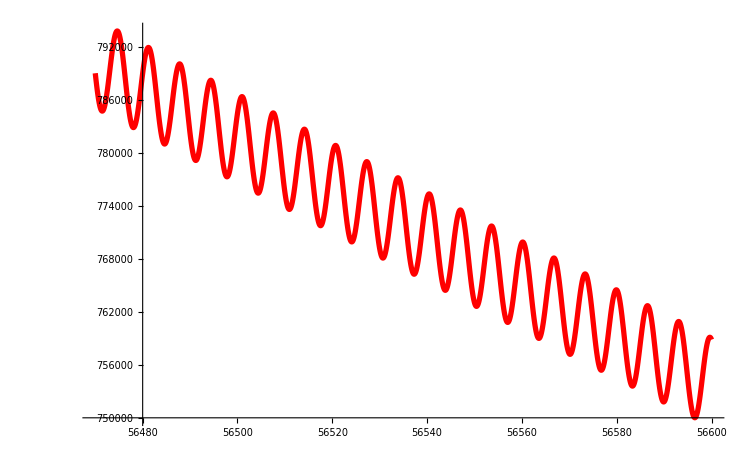

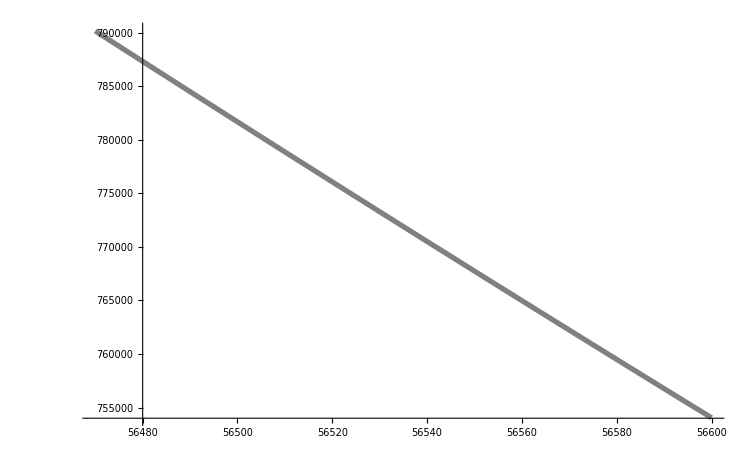

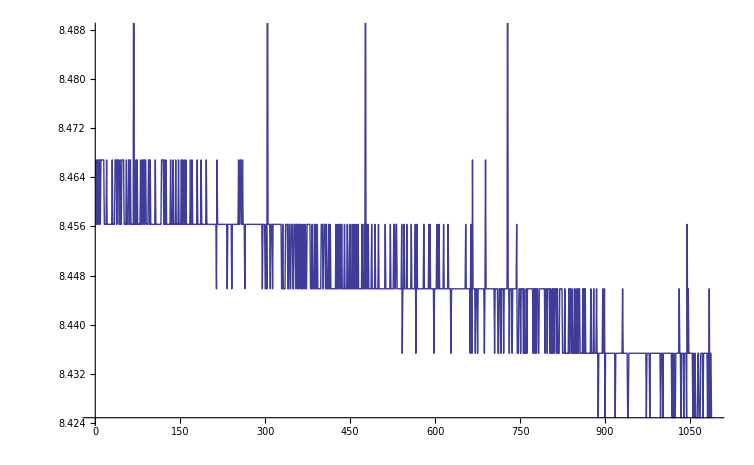

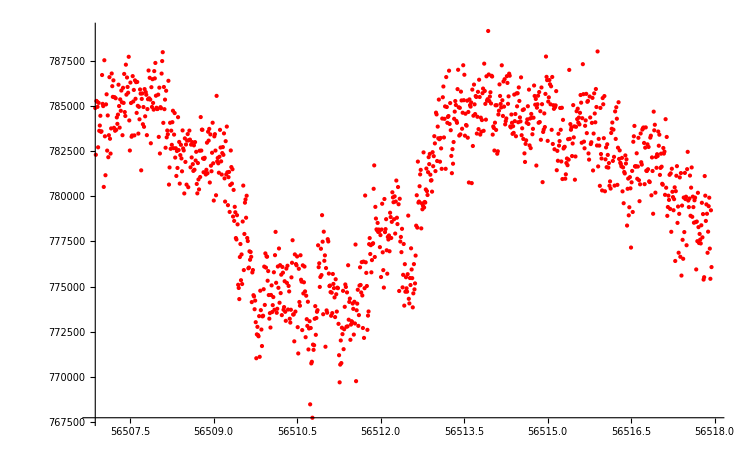

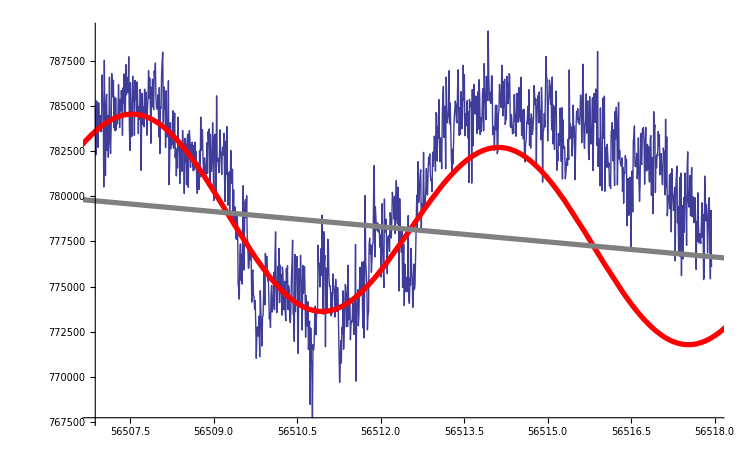

```mathematica
Subscript[N, 0] = 780000;
HalfLife = 1925.20;
T = 1.72154×10^9;
Subscript[N, f] = Subscript[N, 0] ⅇ^(-(Log[2](t -56506))/HalfLife) + 5000Sin[(6t)/(2π)+2/8π];
Subscript[N, k] = Subscript[N, 0] ⅇ^(-(Log[2](t -56506))/HalfLife) ;
data = Import["/Users/spenceraxani/Documents/499_Thesis/data/datapack/L2-008_germanium_data.txt","Table"];
A = ListLinePlot[data,Joined->True]
decay = Plot[Subscript[N, f],{t,56470,56600},PlotStyle->{{Thickness[0.005],Red}}]
decay2 = Plot[Subscript[N, k],{t,56470,56600},PlotStyle->{{Thickness[0.005],Gray}}]
deadtime = Import["/Users/spenceraxani/Documents/499_Thesis/data/datapack/L2-008_germanium_dead_time.txt","Table"];
B=ListPlot[deadtime,Joined->True]

Show[ListPlot[data,PlotStyle->Red],Plot[parabola,{x,0,5000}]]
Show[A,decay, decay2]
```